```mathematica
SetOptions[ListPlot, AspectRatio-> 0.4, Filling->Axis, ClippingStyle->Red, PlotMarkers->Automatic, Mesh->All,Joined->True];
```

```mathematica
V∞=150;(*[m]*)
α = 5 * π/180; (*[rad]*)
b = 15; (*[m]*)
Sw = 10;(*[m^2]*)
twist075=-1*π/180;(*[rad]*)
λ= 0.7;
Cr=2*Sw/b/(λ+1);(*[m]*)
```

```mathematica
a=5.7;(*[1/rad]*)
α0=1.5*π/180;(*[rad]*)
```

```mathematica
n=10;
eta = Table[N[-Cos[(2*y/b+1)*π/2]*b/2],{y,-b/2,b/2,b/(n-1)}]; 
eta[[1]] = (0.75*eta[[1]]+0.25*eta[[2]]);
eta[[-1]] = (0.75*eta[[-1]]+0.25*eta[[-2]]);
eta
```

{-7.38692,-7.04769,-5.74533,-3.75,-1.30236,1.30236,3.75,5.74533,7.04769,7.38692}

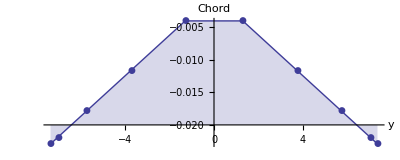

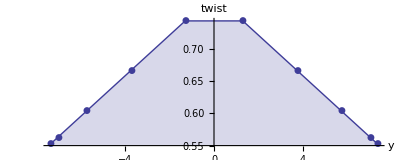

```mathematica
twist = Table[Abs[2*y/b]*twist075*4/3,{y,eta}];
chord = Table[Cr*(1-(1-λ)*2*Abs[y]/b),{y,eta}];
ListPlot[MapThread[List,{eta,twist}],AxesLabel->{"y","Chord"}, Filling-> Axis, Mesh-> All, Joined->True]
ListPlot[MapThread[List,{eta,chord}],AxesLabel->{"y","twist"}, Filling-> Axis, Mesh-> All, Joined->True]
```

```mathematica
theta = Table[ArcCos[-2*y/b],{y,eta}];
m=Table[Table[Sin[j theta[[i]]] ((4 b)/(a chord[[i]] Sin[theta[[i]]])+j),{j,1,n}],{i,1,n}];
B = Table[((α-α0)+twist[[i]])*Sin[theta[[i]]],{i,1,n}]; 
A = LinearSolve[m,B]
```

{0.00275199,-1.47635×10^-19,-0.000859355,1.21656×10^-19,0.0000986869,-2.68142×10^-20,-0.0000468776,-4.6127×10^-20,-0.000011669,2.90517×10^-20}

```mathematica
Γ=Table[0,{i,1,n}];
αi=Table[0,{i,1,n}];
For[i=1,i≤n,i++,
Γ=Γ+A[[i]]*Sin[i * theta]; 
αi=αi+ i*A[[i]]*Sin[i*theta]/Sin[theta];
]
```

```mathematica
Γ=Prepend[Γ,0]; Γ=Append[Γ,0];
αi=Prepend[αi,α-α0+twist[[0]]]; αi=Append[αi,α-α0+twist[[0]]];
eta=Prepend[eta,-b/2];eta=Append[eta,b/2];
```

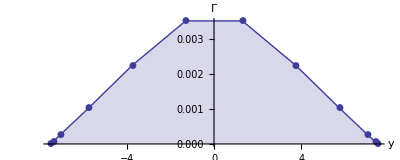

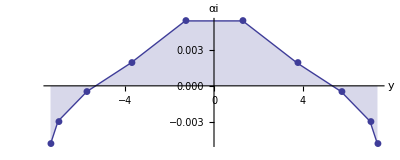

```mathematica
ListPlot[MapThread[List,{eta,Γ}],AxesLabel->{"y","Γ"}, Filling-> Axis, Mesh-> All, Joined->True]
ListPlot[MapThread[List,{eta,αi}],AxesLabel->{"y","αi"}, Filling-> Axis, Mesh-> All, Joined->True]
```

```mathematica
L = NIntegrate[Interpolation[MapThread[List,{eta,Γ}],InterpolationOrder->2][y],{y,-b/2,b/2}]*2*b*V∞
```

144.675

```mathematica
Di= NIntegrate[Interpolation[MapThread[List,{eta,Γ*αi}],InterpolationOrder->2][y],{y,-b/2,b/2}]*2*b*V∞
```

0.498034